```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
data=Import["raw_data.csv","Dataset",HeaderLines->1];
```

```mathematica
r=Normal[data[All,"x"]];
n=Normal[data[All,"y"]];
err=Normal[data[All,"err"]];
```

```mathematica
parabola=
ReplaceAll[p0*x^2+p1*x+p2,{p0->0.0001261,p1->-0.002145,p2->0.4325}];
```

```mathematica
l=0.03 (* Ticks Length *);
```

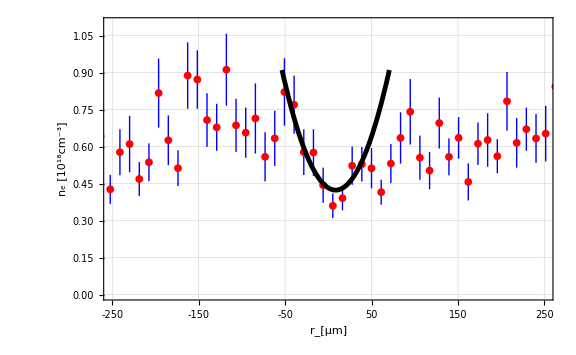

```mathematica
parabolic=Show[{
ListPlot[
Thread[{r,MapThread[Around,{n,err}]}],
IntervalMarkers->"Fences",
IntervalMarkersStyle->{Thick,Blue},
PlotMarkers->{Automatic, 8},
PlotStyle->Red
,PlotRange->{{-250,250},{0,1.1}}
,
Frame->True
,
FrameTicks->{{Automatic,None},{Table[50j,{j,-5,5}],None}}
,
FrameLabel->{Style["r_[µm]",FontFamily->"Latin Modern Roman 10",Large,Black],Style["n_e [10^18cm^-3]",FontFamily->"Latin Modern Roman 10",Large,Black]},
FrameTicksStyle->Directive[Black,FontSize->20,FontFamily->"Latin Modern Roman 10",Thick]
,GridLines->Automatic
]
,
Plot[parabola,{x,-250,250},PlotStyle->Directive[Thickness->0.006,Black],PlotRange->{0,0.91}]
}
,
ImageSize->Large]
```

```mathematica
Export["parabolic.png",parabolic]
Export["parabolic.pdf",parabolic]
```

parabolic.png

parabolic.pdf

x axis label: Capillary radius, [um]
y axis label: Plasma Density, [10^17 cm^(-3)]

```mathematica
((#*0.03)/5.4)^(3/2)&[70]
```

0.242515